```mathematica
UnitConvert[Quantity[1,"amu"],"a.u."]
```

Quantity::timeout: A network operation for Quantity timed out. Please try again later.

Quantity::unkunit: Unable to interpret unit specification amu.

UnitConvert[Quantity[1,amu],a.u.]

```mathematica
data={{1,3.8454},{2,7.6906},{3,11.5355},{4,15.3799},{5,19.2238},{6,23.06685}};
f=Fit[data,{x,x^3},x]
```

3.84539 x-0.0000255536 x^3

```mathematica
3.8453948842823853/2
```

1.9227

```mathematica
0.000025553613053586788/4
```

6.3884×10^-6

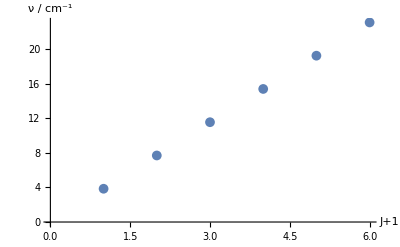

```mathematica
p1=ListPlot[data,PlotMarkers->{Automatic,10}, AxesLabel->{"J+1","ν / cm^-1"}]
```

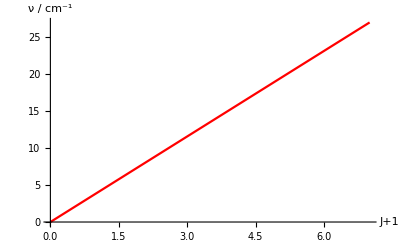

```mathematica
p2=Plot[f,{x,0,7},PlotStyle->Red, AxesLabel->{"J+1","ν / cm^-1"}]
```

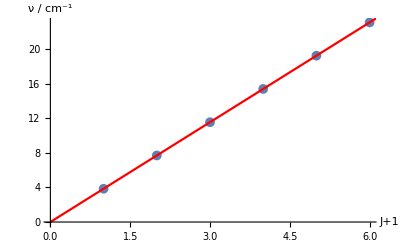

```mathematica
Show[p1,p2]
```